# NEWTON’S LAWS

## PreLab submission with a pass grade is required to begin the lab. Must be submitted no later than right before the start of the corresponding lab session.

Name: Aryan Malhotra
Section: H4
Date: 9/24/24

## Purpose

Purpose of the lab is to understand the concepts of Newton’s Laws of motion.
But before that we need to get familiar with the concepts of linear fit and correlation coefficients. This prerequisite assignment is designed to do that.

## Readings

Checking relationship with a graph
Coefficient of linear correlation Sec. .009.3.00

### Some References to Mathematica Commands

ErrorListPlot, LinearModelFit, RSquared

## Procedure

Getting the data from Students’ Scores data from the Table 9.3 on the page 218 John R. Taylor, we calculate the correlation coefficient for a linear fit.
Then we finish up with a discussion of the results.

## Dialog:

### Step 1.

- Save the data in a two column format [you can use Insert Table from the top menu].

```mathematica
hve={{90, 90}, {60, 71}, {45, 65}, {100, 100}, {15, 45}, {23, 60}, {52, 75}, {30, 85}, {71, 100}, {88, 80}};
Grid[Prepend[hve,{"Homework","Exam"}], Frame -> All]
```

Homework | Exam
90 | 90
60 | 71
45 | 65
100 | 100
15 | 45
23 | 60
52 | 75
30 | 85
71 | 100
88 | 80

### Step 2.

- Find the linear fit to your data using Fit[data,{1,x},x].  
- Plot your data and its linear fit together using Show[] command.

50.4698+0.463941 x

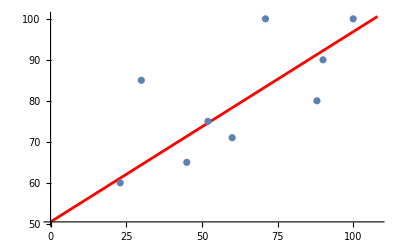

```mathematica
line=Fit[hve, {1,x},x]
Show[Plot[line,{x,0,108},PlotStyle->Red],ListPlot[hve, AxesLabel->{"Homework","Exam"}]]
```

### Step 3.

- Calculate the correlation coefficient for the linear fit and explain its meaning.

```mathematica
n = Length[hve];
homeworkGrades = {};
examGrades = {};
Do[x=hve[[i]];
AppendTo[homeworkGrades, Part[x, 1]];AppendTo[examGrades, Part[x,2]],
{i,1,n}];
(*Just Create a List of Grades in Homework and Exam*)

homeworkMean = Sum[homeworkGrades[[i]],{i,1,n}]/n;
examMean = Sum[examGrades[[i]], {i,1,n}]/n;

(*Calculating the correlation coefficient*)
corcoeff=(Sum[(homeworkGrades[[i]]-homeworkMean)*(examGrades[[i]]-examMean), {i, 1, n}])/ Sqrt[((Sum[(homeworkGrades[[i]]-homeworkMean)^2, {i, 1, n}])*(Sum[(examGrades[[i]]-examMean)^2, {i, 1, n}]))];

N[corcoeff]
```

0.780725

The correlation coefficient  for the linear fit is about 0.78.
The correlation coefficient is calculated as the ratio σ_xy/(σ_x σ_y). Meaning, how close is the covariance of a set of data for 2 particular variables to the product of the variance of the 2 variables.

The Covariance describes how correlated 2 variables are. It’s the sum ∑(x_i- x̄)(y_i- ȳ) looped over the entire data. If the variables are not related, it follows probabilistically that both the terms in the sum can have any spread of magnitudes and sign. Hence, over a large dataset, the values should cancel each other out. Hence, for unrelated variables, the covariance is 0 (at least for the limiting case of infinite values).
For a perfectly linear correlation, y = b + ax and hence ȳ = b + ax̄. And so it follows that y_i-ȳ = B(x_i-x̄) .
Meaning that since both the terms are related, the probabilistic cancelation doesn’t happen, instead, the covariance is always positive. 
So for a correlated dataset, covariance is non zero.

But how non zero?
How far away from zero?

Algebraically, it also turns out that the ratio equating to the correlation coefficient is just ±1.
So correlation coefficient is a metric that helps us quantify the correlation in a more meaningful (but not perfect) way in which values closer to 1 mean the variables show a trend highly similar to that of a linear relation while values of the correlation coefficient closer to 0 mean that the variables have no correlation at all.

Essentially, it provides us a scale to compare the covariance of a data to the standard deviations in our variables to help us understand how related the two variables of interest are.

Rutgers 275 Classical Physics Lab
“Newton’s Laws”
Contributed by Maryam Taherinejad and Girsh Blumberg ©2014